#### Data

```mathematica
Clear["Global`*"]
(*units and constants for trap depth mostly*)
kHz=10^3;
nm=10^-9;
mK=10^-3;
uK=10^-6;
us=10^-6;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
λtrap=976 nm;
m=132.90545 amu;23amu;
Needs["ErrorBarLogPlots`"];
SetDirectory[NotebookDirectory[]];

params=Import["params.csv"][[1]];

(*
1=Na|Na+Cs;
2=Cs|Na+Cs;
3=Na|Na;
4=Cs|Cs;
*)
survNonInt=Transpose[Import["surv.csv"]][[;;,4]]; 
survInt=Transpose[Import["surv.csv"]][[;;,2]]; 

survNonIntErr=Transpose[Import["survErr.csv"]][[;;,4]];
survIntErr=Transpose[Import["survErr.csv"]][[;;,2]];

(*only take the first half.. what are the 2 halves??*)

i=1;
len=32; (*length of one part*)
dataNonInt=Thread[{Thread[{(params-((i-1)len+1)) ,survNonInt}],ErrorBar[#]&/@survNonIntErr}][[(i-1)len+1;;i len]];
dataInt=Thread[{Thread[{(params-((i-1)len+1)) ,survInt}],ErrorBar[#]&/@survIntErr}][[(i-1)len +1;;i len]];
```

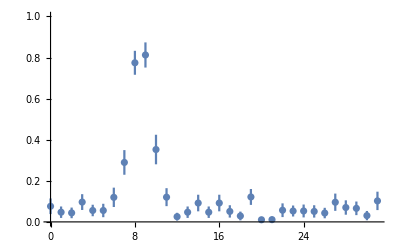

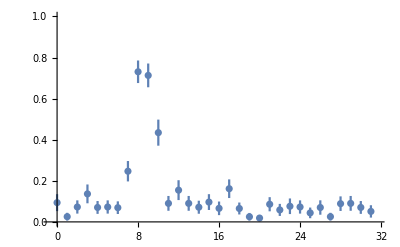

```mathematica
ErrorListPlot[dataInt,PlotRange->{All,{0,1}}]

ErrorListPlot[dataNonInt,PlotRange->{All,{0,1}}]
```

```mathematica
{{24.721855123160815,0.07560601525416466}/{8.457476777117991,0.7322284426830994}}
```

{{2.92308,0.103255}}

```mathematica
(*sideband ratios (Interacting, noninteracting)
non int vs int doesn't seem to make a difference*)
Na3={ .24,.22};
Na2={ .06,.12};
Na1={.11,.13};

Cs3={.19,.18};
Cs2={.11,.09};
Cs1={.08,.1};

(*nbar*)
#/(1-#)&/@Na1;
#/(1-#)&/@Na2;
#/(1-#)&/@Na3;
nbarNa={Mean[%%%],Mean[%%],Mean[%]};
PnNa=Transpose[#^n/(#+1)^(n+1)&/@nbarNa/.n->{0,1,2}];
#/(1-#)&/@Cs1;
#/(1-#)&/@Cs2;
#/(1-#)&/@Cs3;
nbarCs={Mean[%%%],Mean[%%],Mean[%]};
PnCs=Transpose[#^n/(#+1)^(n+1)&/@nbarCs/.n->{0,1,2}];
"nbar Na"
nbarNa
"Pn Na for n=0,1,2"
PnNa

"nbarCs"
nbarCs
"Pn Cs for n=0,1,2"
PnCs
```

nbar Na

{0.13651,0.100097,0.29892}

Pn Na for n=0,1,2

{{0.879886,0.909011,0.76987},{0.105686,0.08271,0.17717},{0.0126944,0.0075257,0.0407721}}

nbarCs

{0.0990338,0.111248,0.22704}

Pn Cs for n=0,1,2

{{0.90989,0.899889,0.814969},{0.0819901,0.0900889,0.150794},{0.00738812,0.0090189,0.0279016}}

# also try overdriving but with interference from a component (=gnd state fraction) shifted by xyz kHz to left factor of 2pi??? expected shift:-13(7)kHz offs valid? is there interference? yes but waste of time to model...should just optimize OP does a nearby molecular state cause shift??? omega vs 2pi???